# Different Couplings scalar-Gauss-Bonnet gravity spontaneous scalarization

```mathematica
Quit[];
```

## Spontaneous scalarization (ℱ’[0]=0)

```mathematica
SetDirectory[NotebookDirectory[]]; (*imposto la directory del current evaluation notebook*)
```

```mathematica
(*Loading the system of equations from auxiliary file*)(*importo i file contenenti le equazioni differenziali che mi interessano*)
```

```mathematica
EQSEDGB=Import["Needed Files/general_edgb_systemeqs.m"];
backEQS=Import["Needed Files/general_background_eqs.m"];
BEQS=Simplify[backEQS//.{Vf->(0&),α->1/2}];
```

```mathematica
(*Load packages for numerical integration*)
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["GUIKit`"];
```

```mathematica
(*Define the coupling function we will study*)
```

```mathematica
ruleThird={ℱ-> ((η/12#^3)&)};
ruleExponential={ℱ->((η/12(1-Exp[-3/2#^2]))&)};
ruleExpoGen={ℱ->((η/(4*2a)(1-Exp[-a#^2]))&)};
ruleTwoThree={ℱ-> ((η/8#^2+λ/12#^3)&)};
ruleTwoFour={ℱ-> ((η/8#^2+λ/16#^4)&)};
```

## Integration

Background boundary conditions

```mathematica
BCSbckHor=<<"../Stability/Data/expanded_bck_BCS_hor.m";
```

Boundary condition for the background at the horizon. We shall consider only terms up to second order.

```mathematica
bouhor={Sum[Subscript[ai, i](r-1)^i,{i,1,2}],Sum[Subscript[bi, i](r-1)^i,{i,1,2}],Sum[Subscript[fi, i](r-1)^i,{i,0,2}],D[Sum[Subscript[fi, i](r-1)^i,{i,0,2}],r]};
```

#### Integrating funtions

```mathematica
Clear[A,B,ϕ]
```

```mathematica
sGBINT[phic0_,constants_,rmax0_,NHorizons0_,MODEL_]:=(
rh0=1;(*Horizon radius is set to 1 without loss of generality*)
(*Parameters to be used in the integrator*)
rulePARAM={MaxSteps->Infinity,PrecisionGoal->15,AccuracyGoal->15,InterpolationOrder->All,Method->"StiffnessSwitching"};
(*How far from the horizon we will start our integrations*)
ϵ=2*10^-16;
BChorrule=BCSbckHor//.F->ℱ//.MODEL;
ruBChor=BChorrule//.constants/.Subscript[fi, 0]->phic0/.Subscript[ai, 1]->rh0/.rh->rh0;

BOU=Thread[{A[r],B[r],ϕ[r], ϕ'[r]}==(bouhor//.ruBChor/.Subscript[fi, 0]->phic0/.Subscript[ai, 1]->rh0/.rh->rh0)]/.r->rh0+ϵ;

BCS=BOU;
(*Numerical integration*)
sol=NDSolve[
Union[Union[{BEQS[[2]]==0,BEQS[[1]]==0, BEQS[[3]]==0}//.F->ℱ//.MODEL/.constants],BCS],
{A,B,ϕ},
{r,rh0+ϵ,rmax0},
rulePARAM][[1]];

(* Solutions of the numerical integration.
Observe that Λ, which is the radial metric function that appears in the spheric simmetric metric, can be obtained from ϕ and Υ according to 
 Eqs. (A1) and (A2) from Kanti+, here generalized*)
ϕsol=ϕ[r]/.sol;
Dϕsol=D[ϕsol,r];
Asol=A[r]/.sol;
DAsol=D[Asol,r];
Bsol=B[r]/.sol;
DBsol=D[Bsol,r];
(*Values of variables at infinity*)
ϕinf=ϕsol/.{r-> rmax0};
Ainf=Asol/.{r-> rmax0};
Binf=Bsol/.{r-> rmax0};
Asolshift=Asol/Ainf;

(*Extract physical parameters of the BH solution*)
PhysicalParams=NSolve[{
Asolshift==1-(2 M)/r+((M Q^2)/(12 r^3)),
ϕsol==ϕ0+Q/r+(M Q)/r^2+((32 M^2 Q-Q^3)/(24 r^3)),
D[ϕsol,r]==D[ϕ0+Q/r+(M Q)/r^2,r]&&M≥ 0 }/.{r->rh0*NHorizons0},{ϕ0,Q,M}][[1]];

(*NOTA: entrambe le costanti di accoppiamento η e λ hanno (dimensione [length])^2, mentre il campo scalare à adimensionale in tale trattazione e lo scalare di Gauss-Bonnet (è [length])^-4*)
(*Nell'output restituisco l'esponenziale delle funzioni metriche Υ e Λ, che chiamo A[r] e B[r]*)

(*Output: ϕ0, ϕinf, Q/M, η/M^2, M, ϕsol, Dϕsol, A[r], A'[r], B[r], B'[r]*)

{ϕ0/.PhysicalParams,
ϕinf,
(Q/M)/.PhysicalParams,
(η/M^2)/.constants/.PhysicalParams,
M/.PhysicalParams,
ϕsol,
Dϕsol,
Asol/Ainf,
DAsol/Ainf,
Bsol(*/Binf*),
DBsol(*/Binf*)
}
);
```

#### Graphics of solutions

```mathematica
(*η0=0.7;
η1=4.6;
η2=12.7;
phih0=0.5092521002504304;
phih1=0.07622939688650629;
phih2=0.006804176641385111;
BCKGRND0=sGBINT[phih0,η0,10^12,150,ruleThird];
BCKGRND1=sGBINT[phih1,η1,10^12,150,ruleThird];
BCKGRND2=sGBINT[phih2,η2,10^12,150,ruleThird];
ϕbck=BCKGRND0[[6]];
ϕbck1=BCKGRND1[[6]];
ϕbck2=BCKGRND2[[6]];
Show[Plot[Legended[ϕbck/phih0,"η=0.7"],{r,1,10},Frame->True,AspectRatio->1/2,FrameLabel->{"r","ϕ(r)"},LabelStyle->Directive[Black,Medium],PlotRange->{-0.5,1}],Plot[Legended[ϕbck1/phih1,"η=4.6"],{r,1,10},PlotRange->{-0.5,1},PlotStyle->Green,Frame->True,AspectRatio->1/2,FrameLabel->{"r","ϕ(r)"},LabelStyle->Directive[Black,Medium]],Plot[Legended[ϕbck2/phih2,"η=12.7"],{r,1,10},PlotRange->{-0.5,1},PlotStyle->Red,Frame->True,AspectRatio->1/2,FrameLabel->{"r","ϕ(r)"},LabelStyle->Directive[Black,Medium]]]*)
```

```mathematica
(*range={-0.04,0.52};
Show[Plot[Legended[ϕbck,"η=0.7"],{r,1,3},Frame->True,AspectRatio->1/2,FrameLabel->{"r","ϕ(r)"},LabelStyle->Directive[Black,Medium],PlotRange->range],Plot[Legended[ϕbck1,"η=4.6"],{r,1,3},PlotRange->range,PlotStyle->Green,Frame->True,AspectRatio->1/2,FrameLabel->{"r","ϕ(r)"},LabelStyle->Directive[Black,Medium]],Plot[Legended[ϕbck2,"η=12.7"],{r,1,3},PlotRange->range,PlotStyle->Red,Frame->True,AspectRatio->1/2,FrameLabel->{"r","ϕ(r)"},LabelStyle->Directive[Black,Medium]]]*)
```

```mathematica
(*η0=12;
phi0=0.09;
prova={η->0.4,a->3};
BCKGRND0=sGBINT[phi0,prova,10^12,150,ruleExponential2];
Plot[BCKGRND0[[6]]/phi0,{r,1,10},PlotRange->{{1,10},{-1,1}}]*)
```

```mathematica
(*BCKGRND0[[8]]*)
```

```mathematica
(*Ainf*)
```

```mathematica
(*Plot[{BCKGRND0[[6]],BCKGRND0m[[6]]},{r,1,10}]*)
```

## ROOT FINDING

### Regularity and physical conditions

From regularity condition we extract the maximum value of Φ_h for which scalarized sol is possible. The beginning of the range in which we can search for the value that triggers the scalarization (at fixed coupling constants) is 0 for Z_2 symmetric coupling functions

```mathematica
(*From regularity condition we extract the maximum value of Subscript[Φ, h] for which scalarized sol is possible.*)
Findϕhmax[coupConst_,MODEL_]:=
(
rh0=1;

(*Solve the real/regularity condition*)
ϕhsols=ϕh/.Solve[(1-96 D[ℱ[ϕ[r]],ϕ[r]]^2/(rh)^4/.MODEL/.coupConst/.{ϕ[r]-> ϕh,rh->rh0})==0,ϕh];
ϕhpositive={};
If [MODEL==ruleTwoFour||(λ/.coupConst)<0,
(*Select the positive value of ϕh*)
For[i=1,i<=Length[ϕhsols],i++,
If[Re[ϕhsols[[i]]]>0,
ϕhpositive=AppendTo[ϕhpositive,ϕhsols[[i]]]]];
If[Im[ϕhpositive[[1]]]!=0, ϕhchosen={0,0,ϕhpositive[[Length[ϕhpositive]]]},ϕhchosen=ϕhpositive]];

If [(λ/.coupConst)>=0,
(*Select the positive value of ϕh*)
For[i=1,i<=Length[ϕhsols],i++,
If[Re[ϕhsols[[i]]]>0,
ϕhpositive=AppendTo[ϕhpositive,ϕhsols[[i]]]]];

ϕhchosen={0,0,ϕhpositive[[Length[ϕhpositive]]]}];


ϕhchosen
);
```

I want to find the value of the coupling constant η at which the function 1-96( ℱ'[ϕ])^2, the one in the sqrt in regularity condition, has  real zeroes

```mathematica
RealZero[ai_,MODEL_]:=(
nn=10000;

Do[
etamax=6;
etatmp=j/nn etamax;
If[MODEL==ruleExpoGen,
try={η->etatmp,a->ai}];
If[MODEL==ruleTwoThree||MODEL==ruleTwoFour,
Print["ok"];
try={η->etatmp,λ->ai*etatmp}];
ret=ϕ/.NSolve[1-96( ℱ'[ϕ])^2==0/.MODEL/.try/.rh->1,ϕ][[1]];
If[Im[ret]==0,return=etatmp;Break[]],{j,1,nn}];
N[return]
);
```

```mathematica
FindϕhmaxExp[constants_,MODEL_,limit_]:=
(
rh0=1;
(*Solve the real/regularity condition*)
(*I saw that the solution of 1-96 D[ℱ[ϕ],ϕ]^2/(rh)^4==0 is Real only for (- 1)/(2 η0^2)>-1/E, but if we plot the function we see that for η<√(E/2) the function is always positive, so there are no limits to the value of ϕh up to that point*)
If[(η/.constants)>=limit,
ϕhsols=ϕ/.NSolve[1-96 ( ℱ'[ϕ])^2/(rh)^4==0/.MODEL/.constants/.rh->rh0,ϕ],
ϕhsols={0,0}];
(*Select the positive value of ϕh. Ci sono sufficienti questi per l'invarianza sotto Φ->-Φ*)
ϕhchosen1=Select[ϕhsols,#>=0&]
);
```

{0.400733,0.599267,1.2001}

{-0.200104,0.400733,0.599267,1.2001}

{0.400733,0.599267,1.2001}

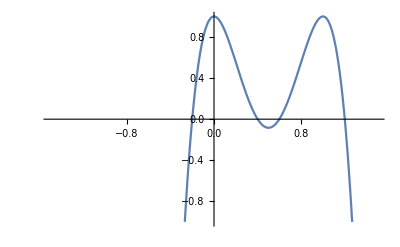

```mathematica
mult=-1;
eta=1.7;
prova={η->eta,λ->mult*eta};
coupling=ruleTwoThree;

Findϕhmax[prova,coupling]
ϕhsols
ϕhpositive
Plot[1-96( ℱ'[ϕ])^2/.coupling/.prova/.rh->1,{ϕ,-10,10},PlotRange->{{-1.5,1.5(*Findϕhmax[prova,coupling][[1]]+0.5*)},{-1,1}}]
```

```mathematica
ϕhsols
```

{-0.200104,0.400733,0.599267,1.2001}

Scal:   η/rh^2, λ/rh^2  ->  ϕh   with ϕinf=0.   If for the chosen η there is no scalarization, ϕh=0; if there is scalarization, ϕh is the value corresponding to the scalarized solution, i.e. the one to which corrisponds the non trivial solution with ϕinf=0.
Ricopio input/output della sGBINT
Input: 	ϕh, coupling constants, rmax, Nh, rule
output:	rh/M, ϕh, ϕinf, Q/M, M, ϕ[r], [r] , Λ[r]

```mathematica
Scal[coupConst_,inizio_,MODEL_]:=
(
nn=60;
rh0=1;
NUM=100;
RMAX=10^10;
ϕhzeros=N[Findϕhmax[coupConst,MODEL]];(*Array of three elements*)
If[ϕhzeros[[1]]==0,
ϕhmax=ϕhzeros[[3]],ϕhmax= ϕhzeros[[1]]];
dϕh=ϕhmax/nn;
tabϕh={};
Do[ϕh1=ii dϕh;
tabϕh=AppendTo[tabϕh,N[sGBINT[ϕh1,coupConst,RMAX,NUM,MODEL][[2]] ]],
{ii,1,nn-2}];
NN=Length[tabϕh];
(*Ora devo verificare che esista una soluzione di ϕinf = 0 diversa da quella banale e per farlo guardo se gli estremi di ϕinf sono di segno concorde o no.*)
If[tabϕh[[1]]*tabϕh[[NN]]>=0,out=0, Do[If[tabϕh[[ii]]*tabϕh[[ii+1]]<0,out= dϕh(tabϕh[[ii+1]]ii-tabϕh[[ii]](ii+1))/(tabϕh[[ii+1]]-tabϕh[[ii]])],{ii,1,NN-1}]];

If[
out==0;ϕhzeros[[1]]!=0,
ϕhmin=ϕhzeros[[2]];
ϕhmax=ϕhzeros[[3]];
dϕh=(ϕhmax-ϕhmin)/nn;

tabϕh={};
Do[ϕh1=ϕhmin+( ii +inizio)dϕh;
phihtmp=N[sGBINT[ϕh1,coupConst,RMAX,NUM,MODEL]][[2]] ;
If[phihtmp>4,Break[],
tabϕh=AppendTo[tabϕh,phihtmp]],
{ii,1,nn-30}];
NN=Length[tabϕh];
(*Ora devo verificare che esista una soluzione di ϕinf = 0 diversa da quella banale e per farlo guardo se gli estremi di ϕinf sono di segno concorde o no.*)
If[tabϕh[[1]]*tabϕh[[NN]]>=0,out=0, Do[If[tabϕh[[ii]]*tabϕh[[ii+1]]<0,out= ϕhmin+dϕh(tabϕh[[ii+1]](ii+inizio)-tabϕh[[ii]](ii+inizio+1))/(tabϕh[[ii+1]]-tabϕh[[ii]])],{ii,1,NN-1}]]];
out
(*out è in sostanza il punto medio interpolato trale due soluzioni ϕinf con segno discorde*)
);
```

```mathematica
ScalExp[constants_,inizio_,node_,MODEL_,limit_]:=
(
η0=η/.constants;
nn=60;
rh0=1;
NUM=100;
RMAX=10^10;
ϕhres=N[FindϕhmaxExp[constants,MODEL,limit]];(*2-elements array for the chosen coupling*)
(*Print[ϕhres];*)

If[η0>limit,
dϕh=ϕhres[[1]]/nn;
tabϕh={};
tabϕinfϕh={};
Do[ϕh1=(ii) dϕh;
If[ϕh1!=0,
res=sGBINT[ϕh1,constants,RMAX,NUM,MODEL];
tabϕh=AppendTo[tabϕh,N[res[[2]]]];
tabϕinfϕh=AppendTo[tabϕinfϕh,{ϕh1,N[res[[2]]]}]] ,
{ii,1,nn-1}];
NN=Length[tabϕh]-1;
(*Now I have to check if there is a solution of ϕ different from the trivial one, meaning that it should verify condition Subscript[ϕ, inf]=0*)
If[tabϕh[[1]]*tabϕh[[NN]]>=0,out=0,Print[tabϕh[[1]]*tabϕh[[NN]]]; Do[If[tabϕh[[ii]]*tabϕh[[ii+1]]<=0,out= dϕh(tabϕh[[ii+1]]ii-tabϕh[[ii]](ii+1))/(tabϕh[[ii+1]]-tabϕh[[ii]])],{ii,1,NN}]];

(*Print[tabϕinfϕh];*)
If[ 
(*the commented condition needs to distinguish 1node sol from 0 node, but value of eta that triggers 1 node sol has to be adjusted for each coupling...*)
out==0 (*|| out!=0&& η0>33.7&&node==0,*),
dϕh=10^-3;
tabϕh2={};
tabϕh2=AppendTo[tabϕh2,0];
ϕhmin=ϕhres[[2]];
(*If[η0<38,ϕhmin=ϕhres[[2]],ϕhmin=1.92];*)
Do[ϕh1=ϕhmin+(ii+inizio) dϕh;
If[ϕh1!=0,
res=sGBINT[ϕh1,constants,RMAX,NUM,MODEL];
tabϕh2=AppendTo[tabϕh2,N[res[[2]]]];
If[tabϕh2[[ii]]*tabϕh2[[ii-1]]<0&&tabϕh2[[ii]]<2, out= ϕhmin +dϕh(tabϕh2[[ii]](ii+inizio-1)-tabϕh2[[ii-1]](ii+inizio))/(tabϕh2[[ii]]-tabϕh2[[ii-1]]);Break[]] ],
{ii,2,100000}]
],

dϕh=10^-3;
tabϕh2={};
tabϕh2=AppendTo[tabϕh2,0];
Do[ϕh1=(ii) dϕh;
If[ϕh1!=0,
res=sGBINT[ϕh1,constants,RMAX,NUM,MODEL];
tabϕh2=AppendTo[tabϕh2,N[res[[2]]]];
If[tabϕh2[[ii]]*tabϕh2[[ii-1]]<0&&tabϕh2[[ii]]<2, out=dϕh(tabϕh2[[ii]](ii-1)-tabϕh2[[ii-1]](ii))/(tabϕh2[[ii]]-tabϕh2[[ii-1]]);Break[]] ],
{ii,2,1000}]];

out
(*out è in sostanza il punto medio interpolato trale due soluzioni ϕinf con segno discorde*)
);
```

```mathematica
eta=40.;
{40.,0.9259158173145967,0.6922529720235259,-0.3118018402777398}
phi=ScalExp[{η->eta,a->6},100,1,ruleExpoGen,RealZ]
sGBINT[0.9659158173145967,{η->eta,a->6},RMAX,NUM,ruleExpoGen][[3]]
```

{40.,0.925916,0.692253,-0.311802}

0.963755

1.60492

```mathematica
{40.,0.965916,0.6922529720235259,-0.3118018402777398}
```

0.963755

-0.311802

```mathematica
(*eta=0.739;
mult=-1;
prova={η->eta,λ->mult*eta};
si=sGBINT[0.5,{η->eta,λ->mult*eta},RMAX,NUM,ruleTwoThree]
Scal[prova,0,ruleTwoThree]
ϕhzeros
*)
```

```mathematica
RealZero[3/2,ruleExpoGen]
```

1.1664

=====================================================================================================================================================================================

### Shooting method

mult value needs to be adjusted depending on the constant coupling value, because it sets the beginning of the shooting method of Scal and ScalExp which can be different for different η, since it may make the integration diverge sometimes

#### Shooting method for exponential couplings

```mathematica
RealZero[1.2,ruleExpoGen]
```

1.0428

```mathematica
ηmin=1750;
ηmax=10000;
mult=100;
pts=100;
divided=(ηmax-ηmin)/pts;


Coupling=ruleExpoGen;
node=0;

a0=1.2;
RealZ=1.0428(*RealZero[a0,ruleExpoGen]*);

Branch={};
Monitor[Do[{
ClearAll[ϕ,A,B],
ηtmp=divided*(i-1)+ηmin,
consttmp={η->ηtmp,a->a0};
ϕhtmp=ScalExp[consttmp,mult,node,Coupling,RealZ],
If[ϕhtmp!=0,
result=sGBINT[ϕhtmp,consttmp, 10^10,100,Coupling],result={0,0,0,0,0,0}],
M1=result[[5]],
QsuM=result[[3]],
AppendTo[Branch,{N[ηtmp],N[ϕhtmp],M1,QsuM}],
Print[Branch[[i]]]},{i,1,pts}],i]
```

```mathematica
nomefile=StringJoin[{"Data/Branches/FundExponential_a=1.2_elimins.dat"}];
Save[nomefile,Branch]
```

#### Shooting method for polynomial couplings

```mathematica
λmultiplier=0;
ηmin=2.6474500000000005;
ηmax=3
pts=500;
divided=(ηmax-ηmin)/pts;
inizio=1;
ϵ1=10^-10;
Branch={};

coupling=ruleThird;

Monitor[Do[{
ClearAll[ϕ,A,B],
ηtmp=divided*(j-1)+ηmin;
λtmp=λmultiplier*ηtmp;
consttmp={η->ηtmp,λ->λtmp};
ϕhtmp=Scal[consttmp,inizio,coupling],
If[ϕhtmp!=0,
result=sGBINT[ϕhtmp,consttmp, 10^10,100,coupling],result={0,0,0,0,0,0,0}],
M1=result[[5]];
QsuM=result[[3]];
AppendTo[Branch,{ηtmp,λtmp,ϕhtmp,M1,QsuM}];
Print[Branch[[j]]]},{j,1,pts}],j]
```

3

{2.64745,0.,0.37953,0.513562,0.250457}

{2.64816,0.,0.379417,0.513554,0.25041}

{2.64886,0.,0.379304,0.513546,0.250364}

{2.64957,0.,0.379192,0.513538,0.250318}

{2.65027,0.,0.37908,0.513529,0.250272}

$Aborted

```mathematica
Branch
```

```mathematica
nomefile=StringJoin[{"Data/Branches/FundTwoThree_λ=1η.dat"}];
Save[nomefile,Branch]
```

```mathematica
TABphi3[[1]]
```

{2.64745,0.37953,0.513562,0.128625}

## PLOTS

NOTE: every .dat file reports {coupling constants, phih, Mass, Q/M}, while every .m file {coupling constants, phih, mass, Q} so pay attention to Q or Q/M...    Silly decision I know

```mathematica
SetDirectory[NotebookDirectory[]];
```

Extracts the part of the table corresponding to scalarized solution, giving the corresponding values of η/M^2

```mathematica
(*ReadList["Data/FundTOT1.dat"];
TAB=Branch;
tabelQ={};
tab07Q={};
Do[If[TAB[[i,2]]>0,Massa=( TAB[[i,3]]);tabelQ=AppendTo[tabelQ,{TAB[[i,1]],TAB[[i,2]],Massa,TAB[[i,4]]*Massa}]],{i,1,Length[TAB]}];
Do[If[tabelQ[[i,1]]<=100,(*Print["η=", tabel[[i,1]] ," ","Massa=" ,tabel[[i,3]], " ","Q=", tabel[[i,4]]];*)tab07Q=AppendTo[tab07Q,tabelQ[[i]]]],{i,1,Length[tabelQ]}]
nomefile=StringJoin[{"Data/Branches/Fund1_scalarizedOnly.m"}];
Save[nomefile,tab07Q];*)
```

### Exponential coupling funcitons

#### Fundamental branches

```mathematica
TAB1=ReadList["Data/Branches/Phi3FundBranch.m"][[1]]; 
TAB2=ReadList["Data/Branches/Fund_Exponential.dat"][[1]]; 
TAB3=ReadList["Data/Branches/1Node_Exponential.dat"][[1]];
TAB4=ReadList["Data/Branches/Fund_Exponential_a=3.dat"][[1]]; 
TAB5=ReadList["Data/Branches/Fund_Exponential_a=6.dat"][[1]];
TAB6=ReadList["Data/Branches/FundExponential_a=1.2.dat"][[1]];
TAB1N=ReadList["Data/Branches/1Node_Exponential.dat"][[1]];
ReadList["Data/Branches/Nodes_Exponential_a=3.dat"][[1]]; 
ReadList["Data/Branches/Nodes_Exponential_a=6.dat"][[1]]; 
TABtwothree=ReadList["Data/Branches/FundTwoThree_λ=-η.dat"][[1]];
TABtwothreeUnst=ReadList["Data/Branches/FundTwoThree_λ=1η.dat"][[1]];

(*TAB1c0=Transpose[{tab0[[All,3]]/tab0[[All,1]]^(1/2),Abs[tab0[[All,4]]/tab0[[All,1]]^(1/2)]}];*)
QvsMphi3=Transpose[{TAB1[[All,3]]/TAB1[[All,1]]^(1/2),Abs[TAB1[[All,4]]/TAB1[[All,1]]^(1/2)]}];

QvsMexp=Transpose[{TAB2[[All,3]]/TAB2[[All,1]]^(1/2),Abs[TAB2[[All,4]]*TAB2[[All,3]]/TAB2[[All,1]]^(1/2)]}];
QvsMexpA3=Transpose[{TAB4[[All,3]]/TAB4[[All,1]]^(1/2),Abs[TAB4[[All,4]]*TAB4[[All,3]]/TAB4[[All,1]]^(1/2)]}];
QvsMexpA6=Transpose[{TAB5[[All,3]]/TAB5[[All,1]]^(1/2),Abs[TAB5[[All,4]]*TAB5[[All,3]]/TAB5[[All,1]]^(1/2)]}];
QvsMexpA1=Transpose[{TAB6[[All,3]]/TAB6[[All,1]]^(1/2),Abs[TAB6[[All,4]]*TAB6[[All,3]]/TAB6[[All,1]]^(1/2)]}];

QvsMtwothree=Transpose[{TABtwothree[[All,4]]/TABtwothree[[All,1]]^(1/2),Abs[TABtwothree[[All,5]]*TABtwothree[[All,4]]/TABtwothree[[All,1]]^(1/2)]}];
QvsMtwothreeUnst=Transpose[{TABtwothreeUnst[[All,4]]/TABtwothreeUnst[[All,1]]^(1/2),Abs[TABtwothreeUnst[[All,5]]*TABtwothreeUnst[[All,4]]/TABtwothreeUnst[[All,1]]^(1/2)]}];
```

Q vs M for different couplings fund branches

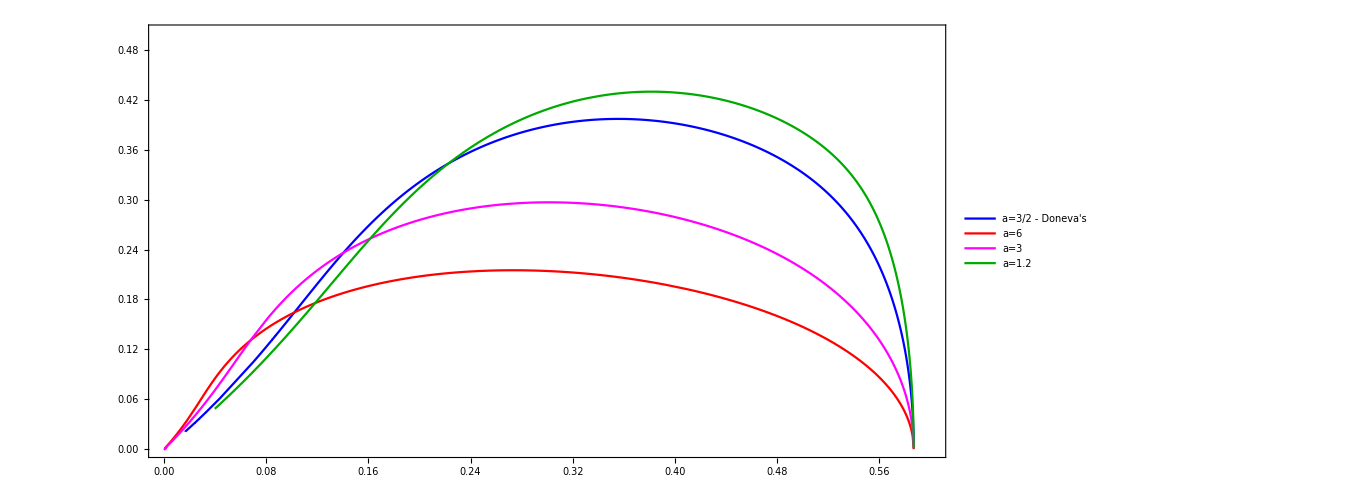
-Graphics-Q/η^(1/2)M/η^(1/2)

```mathematica
Labeled[Show[
(*ListLinePlot[Legended[QvsMphi3,"phi3"],PlotStyle->Green,Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium],PlotRange->{{0,0.9},{-0.01,0.5}}],*)ListLinePlot[Legended [QvsMexp,"a=3/2 - Doneva's" ],PlotStyle->Blue,Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium],PlotRange->{{0,0.6},{0,0.5}}],
ListLinePlot[Legended[QvsMexpA6,"a=6"],PlotStyle->Red,Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium],PlotRange->Full],
ListLinePlot[Legended[QvsMexpA3,"a=3"],PlotStyle->Magenta,Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium]],
ListLinePlot[Legended[QvsMexpA1,"a=1.2"],PlotStyle->Darker[Green],Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium],PlotRange->Full],
(*ListLinePlot[Legended[QvsMtwothree,"Fund two+three"],PlotStyle->Black,Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium]],
ListLinePlot[Legended[QvsMtwothreeUnst,"Fund two+three unst"],PlotStyle->Gray,Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium]],*)
PlotLegends->Placed[Automatic,{Top,Left}],ImageSize->10^3],
{"Q/η^(1/2)","M/η^(1/2)"},{Left,Bottom}]
```

#### Exponential coupling solutions with growing number of nodes

```mathematica
QvsM1nodeexp=Transpose[{TAB3[[All,3]]/TAB3[[All,1]]^(1/2),Abs[TAB3[[All,4]]*TAB3[[All,3]]/TAB3[[All,1]]^(1/2)]}];
QvsM1nodeexpA3=Transpose[{Branch1[[All,3]]/Branch1[[All,1]]^(1/2),Abs[Branch1[[All,4]]*Branch1[[All,3]]/Branch1[[All,1]]^(1/2)]}];
QvsM2nodeexpA3=Transpose[{Branch2[[All,3]]/Branch2[[All,1]]^(1/2),Abs[Branch2[[All,4]]*Branch2[[All,3]]/Branch2[[All,1]]^(1/2)]}];
QvsM3nodeexpA3=Transpose[{Branch3[[All,3]]/Branch3[[All,1]]^(1/2),Abs[Branch3[[All,4]]*Branch3[[All,3]]/Branch3[[All,1]]^(1/2)]}];

QvsMbohnodeexpA6=Transpose[{Branch4A6[[All,3]]/Branch4A6[[All,1]]^(1/2),Abs[Branch4A6[[All,4]]*Branch4A6[[All,3]]/Branch4A6[[All,1]]^(1/2)]}];
QvsM1nodeexpA6=Transpose[{Branch1A6[[All,3]]/Branch1A6[[All,1]]^(1/2),Abs[Branch1A6[[All,4]]*Branch1A6[[All,3]]/Branch1A6[[All,1]]^(1/2)]}];
QvsM2nodeexpA6=Transpose[{Branch2A6[[All,3]]/Branch2A6[[All,1]]^(1/2),Abs[Branch2A6[[All,4]]*Branch2A6[[All,3]]/Branch2A6[[All,1]]^(1/2)]}];
QvsM3nodeexpA6=Transpose[{Branch3A6[[All,3]]/Branch3A6[[All,1]]^(1/2),Abs[Branch3A6[[All,4]]*Branch3A6[[All,3]]/Branch3A6[[All,1]]^(1/2)]}];
```

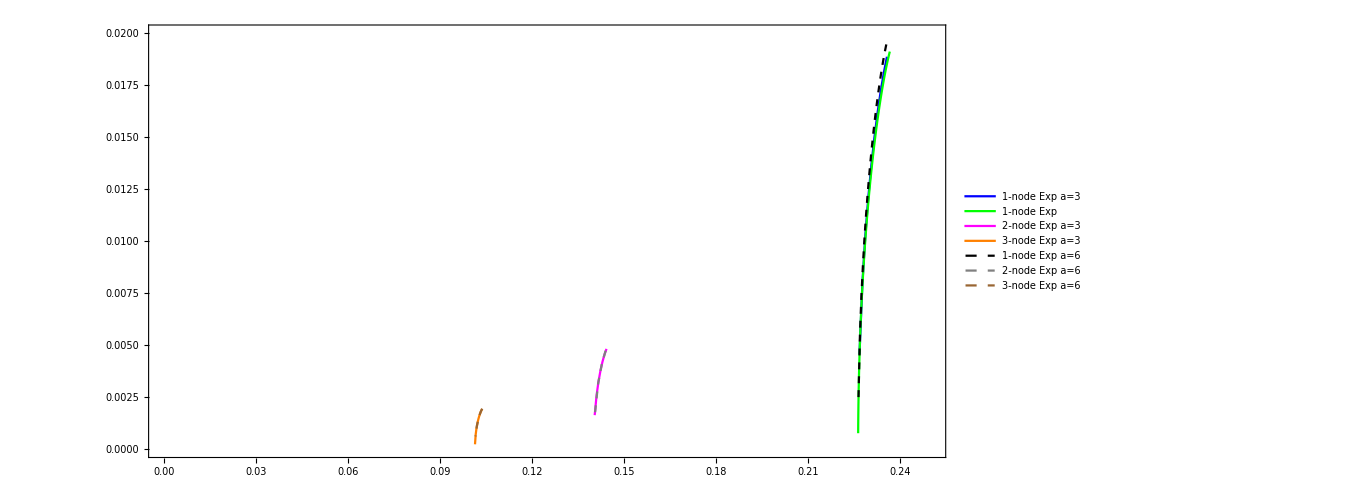
-Graphics-Q/η^(1/2)M/η^(1/2)

```mathematica
Labeled[Show[
(*ListLinePlot[Legended[QvsMphi3,"phi3"],PlotStyle->Red,Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium],PlotRange->{{0,0.35},{0,0.04}}],*)ListLinePlot[Legended[QvsM1nodeexpA3,"1-node Exp a=3"],PlotStyle->Blue,Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium],PlotRange->{{0,0.25},{0,0.02}}],
ListLinePlot[Legended[QvsM1nodeexp,"1-node Exp"],PlotStyle->Green,Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium],PlotRange->Full],
ListLinePlot[Legended[QvsM2nodeexpA3,"2-node Exp a=3"],PlotStyle->Magenta,Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium]],
ListLinePlot[Legended[QvsM3nodeexpA3,"3-node Exp a=3"],PlotStyle->Orange,Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium]],
ListLinePlot[Legended[QvsM1nodeexpA6,"1-node Exp a=6"],PlotStyle->{Black,Dashed},Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium],PlotRange->Full],
ListLinePlot[Legended[QvsM2nodeexpA6,"2-node Exp a=6"],PlotStyle->{Gray,Dashed},Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium]],
ListLinePlot[Legended[QvsM3nodeexpA6,"3-node Exp a=6"],PlotStyle->{Brown,Dashed},Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium]],
ImageSize->10^3],
{"Q/η^(1/2)","M/η^(1/2)"},{Left,Bottom}]
```

### Different power polynomial coupling

```mathematica
TABphi3=ReadList["Data/Branches/Phi3FundBranch.m"][[1]]; 
TABquad=ReadList["Data/Branches/QuadraticFundBranch.m"][[1]]; 
TABquart=ReadList["Data/Branches/QuarticFundBranch.m"][[1]];
```

```mathematica
QvsMphi3=Transpose[{TABphi3[[All,3]]/TABphi3[[All,1]]^(1/2),Abs[TABphi3[[All,4]]*TABphi3[[All,3]]/TABphi3[[All,1]]^(1/2)]}];
QvsMQuadratic=Transpose[{TABquad[[All,3]]/TABquad[[All,1]]^(1/2),Abs[TABquad[[All,4]]*TABquad[[All,3]]/TABquad[[All,1]]^(1/2)]}];
QvsMQuartic=Transpose[{TABquart[[All,3]]/TABquart[[All,1]]^(1/2),Abs[TABquart[[All,4]]*TABquart[[All,3]]/TABquart[[All,1]]^(1/2)]}];
```

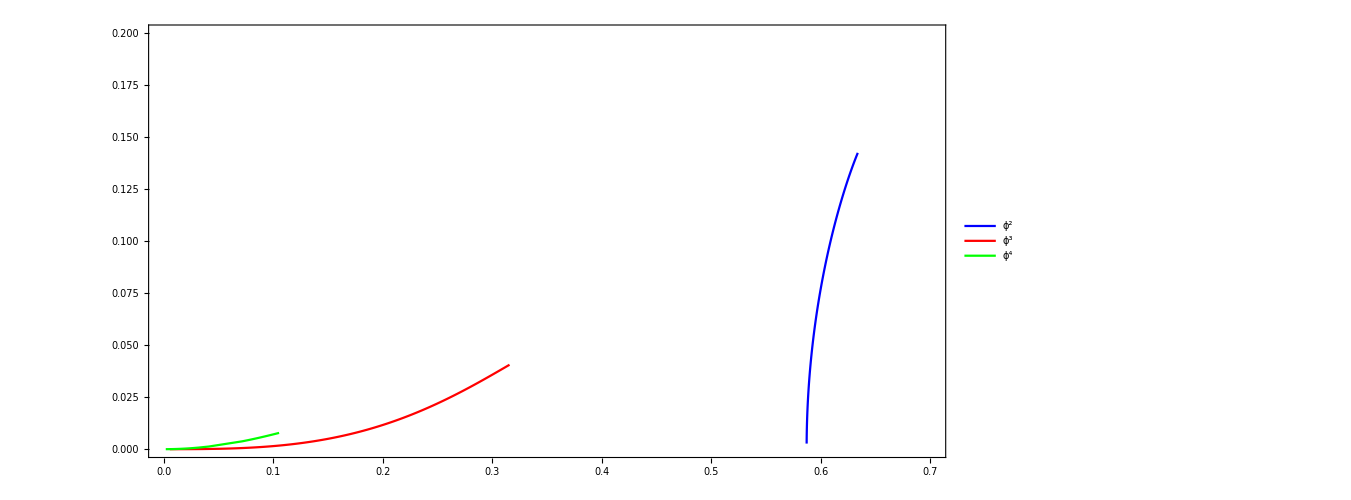
-Graphics-Q/η^(1/2)M/η^(1/2)

```mathematica
Labeled[Show[
ListLinePlot[Legended[QvsMQuadratic,"ϕ^2"],PlotStyle->Blue,Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium],PlotRange->{{0,0.7},{0,0.2}}],
ListLinePlot[Legended[QvsMphi3,"ϕ^3"],PlotStyle->Red,Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium],PlotRange->{{0,0.7},{0,0.2}}],
ListLinePlot[Legended[QvsMQuartic,"ϕ^4"],PlotStyle->Green,Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium],PlotRange->Full],
ImageSize->10^3],
{"Q/η^(1/2)","M/η^(1/2)"},{Left,Bottom}]
```

### Polynomial couplings

Q/η^(1/2) vs M/η^(1/2) for various polynomial couling functions

```mathematica
TABphi3=ReadList["Data/Branches/Phi3FundBranch.m"][[1]]; 
TABquad=ReadList["Data/Branches/QuadraticFundBranch.m"][[1]]; 
TABquart=ReadList["Data/Branches/QuarticFundBranch.m"][[1]];
TAB2405st=ReadList["Data/Branches/Quartic/FundBranch_λ=-0.5η.m"][[1]];
TAB2405st2=ReadList["Data/Branches/Quartic/FundBranch_λ=-0.5η_2.dat"][[1]];
TAB2405=ReadList["Data/Branches/Quartic/FundBranch_λ=0.5η.m"][[1]];
TAB2415st=ReadList["Data/Branches/Quartic/FundBranch_λ=-1.5η.m"][[1]];
TAB2415=ReadList["Data/Branches/Quartic/FundBranch_λ=1.5η.m"][[1]];
TAB2410st=ReadList["Data/Branches/Quartic/FundBranch_λ=-1η.m"][[1]];
TAB2410=ReadList["Data/Branches/Quartic/FundBranch_λ=1η.m"][[1]];
TAB231st=ReadList["Data/Branches/FundTwoThree_λ=-η.dat"][[1]];
TAB231=ReadList["Data/Branches/FundTwoThree_λ=1η.dat"][[1]];
```

```mathematica
QvsMphi3=Transpose[{TABphi3[[All,3]]/TABphi3[[All,1]]^(1/2),Abs[TABphi3[[All,4]]/TABphi3[[All,1]]^(1/2)]}];
QvsMQuadratic=Transpose[{TABquad[[All,3]]/TABquad[[All,1]]^(1/2),Abs[TABquad[[All,4]]/TABquad[[All,1]]^(1/2)]}];
QvsMQuartic=Transpose[{TABquart[[All,3]]/TABquart[[All,1]]^(1/2),Abs[TABquart[[All,4]]/TABquart[[All,1]]^(1/2)]}];
QvsM2405st=Transpose[{TAB2405st[[All,4]]/TAB2405st[[All,1]]^(1/2),Abs[TAB2405st[[All,5]]/TAB2405st[[All,1]]^(1/2)]}];
QvsM2405=Transpose[{TAB2405[[All,4]]/TAB2405[[All,1]]^(1/2),Abs[TAB2405[[All,5]]/TAB2405[[All,1]]^(1/2)]}];
QvsM2415st=Transpose[{TAB2415st[[All,4]]/TAB2415st[[All,1]]^(1/2),Abs[TAB2415st[[All,5]]/TAB2415st[[All,1]]^(1/2)]}];
QvsM2415=Transpose[{TAB2415[[All,4]]/TAB2415[[All,1]]^(1/2),Abs[TAB2415[[All,5]]/TAB2415[[All,1]]^(1/2)]}];
QvsM2410st=Transpose[{TAB2410st[[All,4]]/TAB2410st[[All,1]]^(1/2),Abs[TAB2410st[[All,5]]/TAB2410st[[All,1]]^(1/2)]}];
QvsM2410=Transpose[{TAB2410[[All,4]]/TAB2410[[All,1]]^(1/2),Abs[TAB2410[[All,5]]/TAB2410[[All,1]]^(1/2)]}];
QvsM231st=Transpose[{TAB231st[[All,4]]/TAB231st[[All,1]]^(1/2),Abs[TAB231st[[All,5]]*TAB231st[[All,4]]/TAB231st[[All,1]]^(1/2)]}];
QvsM231=Transpose[{TAB231[[All,4]]/TAB231[[All,1]]^(1/2),Abs[TAB231[[All,5]]*TAB231[[All,4]]/TAB231[[All,1]]^(1/2)]}];
QvsM2405st2=Transpose[{TAB2405st2[[All,4]]/TAB2405st2[[All,1]]^(1/2),Abs[TAB2405st2[[All,5]]*TAB2405st2[[All,4]]/TAB2405st2[[All,1]]^(1/2)]}];
```

```mathematica
Labeled[Show[
ListLinePlot[Callout[QvsMQuadratic,"ϕ^2",Above],PlotStyle->{Black,Dashed},Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium],PlotRange->{{0,0.9},{-0.00001,0.5}},PlotLegends->LineLegend[{Dashed,Line},{"Unstable","Stable"}]],
ListLinePlot[Callout[QvsMphi3,"ϕ^3",Above],PlotStyle->{Orange,Dotted,Thick},PlotLegends->Placed[Automatic,{Right,Top}],PlotRange->Full],
ListLinePlot[Callout[QvsMQuartic,"ϕ^4",Above],PlotStyle->{Magenta,Dotted},PlotLegends->Placed[Automatic,{Right,Top}],PlotRange->Full],
ListLinePlot[Callout[QvsM2405st,"ηϕ^2-0.5ηϕ^4",Above],PlotStyle->{Red,Dashed},PlotLegends->Placed[Automatic,{Right,Top}],PlotRange->Full],
ListLinePlot[Callout[QvsM2405,"ηϕ^2+0.5ηϕ^4",Above],PlotStyle->{Blue,Dashed},PlotLegends->Placed[Automatic,{Right,Top}],PlotRange->Full],
ListLinePlot[Callout[QvsM2415st,"ηϕ^2-1.5ηϕ^4",{Above,Left}],PlotStyle->{Red},PlotLegends->Placed[Automatic,{Right,Top}],PlotRange->Full],
ListLinePlot[Callout[QvsM2415,"ηϕ^2+1.5ηϕ^4",{Above,Left}],PlotStyle->{Blue,Dashed},Frame->True,PlotLegends->Placed[Automatic,{Right,Top}],PlotRange->Full],
ListLinePlot[Callout[QvsM2410st,"ηϕ^2-1.0ηϕ^4",{Above,Left}],PlotStyle->Red,PlotLegends->Placed[Automatic,{Right,Top}],PlotRange->Full],
ListLinePlot[Callout[QvsM2410,"ηϕ^2+1.0ηϕ^4",{Top,Left}],PlotStyle->{Blue,Dashed},PlotLegends->Placed[Automatic,{Right,Top}],PlotRange->Full],
ListLinePlot[Callout[QvsM231st,"ηϕ^2-1.0ηϕ^3",{Left,Above}],PlotStyle->{Green},PlotLegends->Placed[Automatic,{Right,Top}],PlotRange->Full],
ListLinePlot[Callout[QvsM231,"ηϕ^2+1.0ηϕ^3",{Top,Left}],PlotStyle->{Green,Dashed},PlotLegends->Placed[Automatic,{Right,Top}],PlotRange->Full],
ListLinePlot[QvsM2405st2,PlotStyle->{Red},PlotLabels->{"ηϕ^2-0.5ηϕ^4"},PlotRange->Full],
ImageSize->10^3],
{"Q/η^(1/2)","M/η^(1/2)"},{Left,Bottom}]
```

-Graphics-Q/η^(1/2)M/η^(1/2)